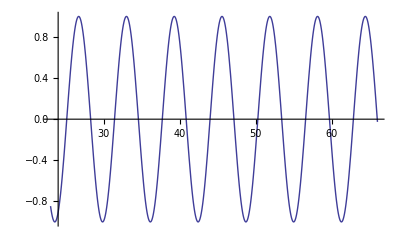

```mathematica
Plot[Sin[x],{x,66,23}]
```

```mathematica
Total[{1,2,3,4,5}]
```

15

```mathematica
PositionInteger[{1,2,3,4,5}/2,_Integer]
```

```mathematica
Position[{1/2,1,3/2,2,5/2},_Integer]
```

{{2},{4}}

```mathematica
H=2736
H*65
```

2736

177840

```mathematica
H*70
```

191520

```mathematica
H/12
```

228

```mathematica
228*65
```

14820

```mathematica
{#,#^2,#^3} &/@ {1,2,3,4}//TableForm
```

1 | 1 | 1
2 | 4 | 8
3 | 9 | 27
4 | 16 | 64

```mathematica
p[x_]:=x+1
```

```mathematica
p[3]
```

4

```mathematica
{#,#^2,#^3,p[#]} &/@ {1,2,3,4}//TableForm
```

1 | 1 | 1 | 2
2 | 4 | 8 | 3
3 | 9 | 27 | 4
4 | 16 | 64 | 5

```mathematica
Grid[Partition[If[PrimeQ[#], Framed[#],#]&/@Range[100],20]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

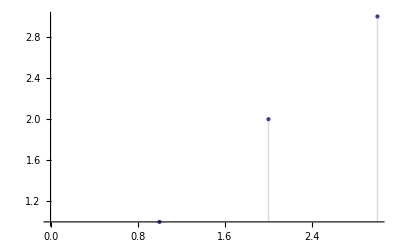

```mathematica
ListPlot[{1,2,3},Filling -> Axis]
```

```mathematica
m={226,
180,
250,
222,
216,
248,
234,
300,
216,
239,
185,
223}
```

{226,180,250,222,216,248,234,300,216,239,185,223}

```mathematica
Total[m]
```

2739

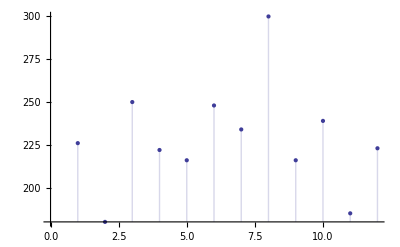

```mathematica
ListPlot[m,Filling->Axis]
```

```mathematica
<<StatisticalPlots`
```

ParetoPlot::shdw: Symbol "ParetoPlot" appears in multiple contexts {"StatisticalPlots`", "Global`"}; definitions in context "StatisticalPlots`" may shadow or be shadowed by other definitions.

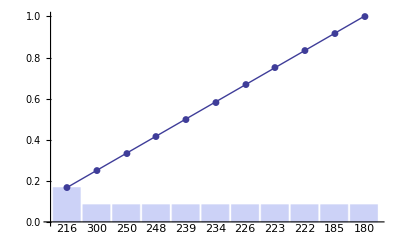

```mathematica
ParetoPlot[m]
```

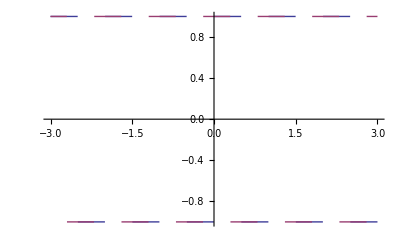

```mathematica
Plot[{SquareWave[x],SquareWave[x+0.2]},{x,-3,3}]
```

```mathematica
Clear[p]
p[x_]:=True/; x>4 &&  PrimeQ[x+3] && PrimeQ[x+7] && !PrimeQ[x+5]
p[x_]:=False

Grid[Partition[If[p[#], Framed[#,{FrameStyle->Blue,Background-> Green}],#]&/@Range[200],20]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100
101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120
121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140
141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160
161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180
181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200

```mathematica
k=Total[m]
```

2739

```mathematica
k-40*52
```

659

{0,0,0,0,0}

```mathematica
data=Table[Random[],{100}]
```

{0.442964,0.762556,0.407813,0.727871,0.265659,0.577134,0.942066,0.349438,0.775165,0.154579,0.247074,0.870079,0.0977774,0.748513,0.963664,0.469149,0.577062,0.739453,0.957924,0.962008,0.135149,0.739222,0.627604,0.831534,0.692185,0.976666,0.21979,0.103664,0.426526,0.399532,0.277725,0.754226,0.651361,0.244953,0.0306511,0.884147,0.553583,0.496441,0.066987,0.414998,0.976521,0.756988,0.109063,0.45299,0.841372,0.0177661,0.48146,0.621456,0.149187,0.0411005,0.261669,0.517792,0.722661,0.641569,0.983944,0.763566,0.0713007,0.396615,0.953293,0.879419,0.517717,0.900175,0.886306,0.464422,0.541196,0.143187,0.777243,0.0114313,0.699824,0.125421,0.295783,0.389975,0.550637,0.0843201,0.0341143,0.872183,0.827976,0.442751,0.0501702,0.108617,0.756675,0.0461363,0.0968771,0.229197,0.238957,0.145962,0.210571,0.764776,0.697761,0.00277494,0.433328,0.753344,0.997937,0.877354,0.137545,0.363369,0.4473,0.793034,0.10343,0.491186}

```mathematica
x=2.5
```

2.5

```mathematica
data2=5*data
```

{2.21482,3.81278,2.03907,3.63935,1.32829,2.88567,4.71033,1.74719,3.87583,0.772893,1.23537,4.3504,0.488887,3.74256,4.81832,2.34574,2.88531,3.69726,4.78962,4.81004,0.675744,3.69611,3.13802,4.15767,3.46092,4.88333,1.09895,0.518318,2.13263,1.99766,1.38862,3.77113,3.2568,1.22477,0.153255,4.42073,2.76792,2.4822,0.334935,2.07499,4.8826,3.78494,0.545316,2.26495,4.20686,0.0888305,2.4073,3.10728,0.745937,0.205502,1.30835,2.58896,3.61331,3.20784,4.91972,3.81783,0.356504,1.98308,4.76647,4.3971,2.58859,4.50087,4.43153,2.32211,2.70598,0.715933,3.88621,0.0571565,3.49912,0.627103,1.47892,1.94988,2.75318,0.4216,0.170572,4.36091,4.13988,2.21376,0.250851,0.543083,3.78337,0.230681,0.484385,1.14599,1.19479,0.729808,1.05286,3.82388,3.4888,0.0138747,2.16664,3.76672,4.98968,4.38677,0.687724,1.81684,2.2365,3.96517,0.517152,2.45593}

```mathematica
hist=Table[0,{5}];Scan[hist[[Ceiling[5#]]]++&,data];hist
```

{24,15,20,22,19}

```mathematica
hist
```

{48,30,40,44,38}

```mathematica
Working with fib

fib[n_]:=fib[n-1]+fib[n-2]
fib[0]=fib[1]=1;
Array[fib,8]
```

fib with Working

{1,2,3,5,8,13,21,34}

{0.000011,0.000015,0.000015,0.000022,0.000035,0.000057,0.000091,0.000146,0.00026,0.000382,0.000637,0.001024,0.001589,0.002579,0.004227,0.006788}

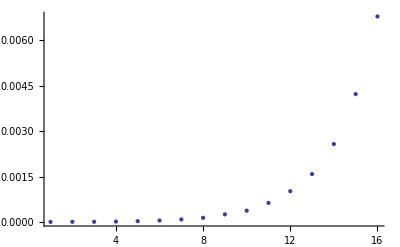

```mathematica
t=Table[Timing[fib[n]][[1]],{n,1,16}]
ListPlot[t]
```

```mathematica
Trace[fib[4],fib[_]]
```

{fib[4],{fib[3],{fib[2],{fib[1]},{fib[0]}},{fib[1]}},{fib[2],{fib[1]},{fib[0]}}}

```mathematica
fib2[n_]:=fib2[n]=fib2[n-1]+fib2[n-2]
fib2[0]=fib2[1]=1
```

1

{0.000032,6.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,7.×10^-6,8.×10^-6,6.×10^-6,6.×10^-6,8.×10^-6,6.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,6.×10^-6,6.×10^-6,0.000124,0.000018,0.000016,0.000017,0.000015,0.000016,0.000017,0.000016,0.000016,0.000016,0.000015,0.000016,0.000015,0.000015,0.000015,0.000016,0.000017,0.000024,0.000015,0.000017,0.000015,0.000015,0.000016,0.000016,0.000016,0.000016,0.000016,0.000015,0.000015,0.00084}

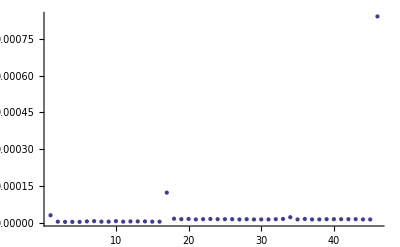

```mathematica
t=Table[Timing[fib2[n]][[1]],{n,1,46}]
ListPlot[t]
```

```mathematica
Trace[fib2[2],fib2[_]]
```

{fib2[2]}

```mathematica
?fib2
```

Global`fib2

```mathematica
ClearAll[x];NestList[f,x,3]
```

{x,f[x],f[f[x]],f[f[f[x]]]}

```mathematica
clearAll[f]
```

```mathematica
clearAll[f,f2]
```

clearAll[f,f2]

```mathematica
f[x_]:=(If[x>5,Return[x+1]];2x)
```

```mathematica
f2[x_]:=(If[x>5,Throw[x+1]];2x)
```

```mathematica
f[7]
```

8

```mathematica
NestList[f,1,6]
Catch[NestList[f2,1,3]]
```

{1,2,4,8,9,10,11}

{1,2,4,8}

```mathematica
Trace[NestList[f,1,6]]
```

{NestList[f,1,6],{f[1],If[1>5,Return[1+1]];2 1,{{1>5,False},If[False,Return[1+1]],Null},{2 1,2},2},{f[2],If[2>5,Return[2+1]];2 2,{{2>5,False},If[False,Return[2+1]],Null},{2 2,4},4},{f[4],If[4>5,Return[4+1]];2 4,{{4>5,False},If[False,Return[4+1]],Null},{2 4,8},8},{f[8],If[8>5,Return[8+1]];2 8,{{8>5,True},If[True,Return[8+1]],Return[8+1],{8+1,9},Return[9]},Return[9],9},{f[9],If[9>5,Return[9+1]];2 9,{{9>5,True},If[True,Return[9+1]],Return[9+1],{9+1,10},Return[10]},Return[10],10},{f[10],If[10>5,Return[10+1]];2 10,{{10>5,True},If[True,Return[10+1]],Return[10+1],{10+1,11},Return[11]},Return[11],11},{1,2,4,8,9,10,11}}

```mathematica
Expand[(1+x)^2*(1+x)^10]
```

```mathematica
k=1+12 x+66 x^2+220 x^3+495 x^4+792 x^5+924 x^6+792 x^7+495 x^8+220 x^9+66 x^10+12 x^11+x^12
```

1+12 x+66 x^2+220 x^3+495 x^4+792 x^5+924 x^6+792 x^7+495 x^8+220 x^9+66 x^10+12 x^11+x^12

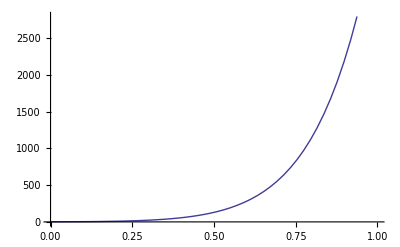

```mathematica
Plot[k,{x,0,1}]
```

```mathematica
23*7
```

161

```mathematica
1/23
```

```mathematica
45*9
```

405

```mathematica
m=Table[i,{i,0,400000000}]
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

$Aborted[]

```mathematica
Plus @@ m
```

800020000

```mathematica
k={1,2,3}
```

{1,2,3}

```mathematica
Plus @@ k
```

6

```mathematica
k=Table[x,{x,42,73}]
```

{42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73}

```mathematica
ClearAll[p,z,y,x]
p[x_,y_,z_]:=x*40+1.5*x*(z-40)/; z>40 && y ==0
```

```mathematica
p[x_,y_,z_]:=x*z/; z<=40 && y ==0
p[x_,y_,z_]:=x*z/; y==1
```

```mathematica
p[55,0,41]
```

2282.5

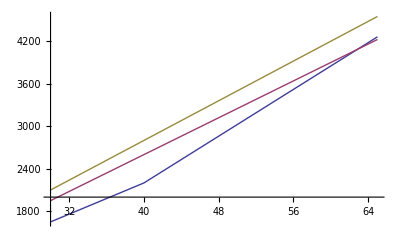

```mathematica
Plot[{p[55,0,x],p[65,1,x],p[70,1,x]},{x,30,65}]
```

```mathematica
55*40+55*1*1.5
```

2282.5

```mathematica
Limit[(1+x)^(1/x),x-> 0]
```

ⅇ

```mathematica
Limit[(1+1/x)^(x),x-> Infinity]
```

ⅇ

```mathematica
p[x_]:=N[(1+x)^(1/x),20]
```

```mathematica
p[2000]
```

1.003807932991071183

```mathematica
LinearProgramming[{1,4},{{1,2}},{3}]
```

{3,0}

```mathematica
Plot[1
```

```mathematica
k[x_,y_,c_]:=x+c*y
```

```mathematica
Plot[k[x,y,4],{x,0,1,y,0,1}]
```

Plot::pllim: Range specification {x, 0, 1, y, 0, 1} is not of the form {x, xmin, xmax}.

Plot[k[x,y,4],{x,0,1,y,0,1}]

```mathematica
k[3,4,4]
```

19

```mathematica
Flatten[Table[{x,y},{x,0,1},{y,0,1}],1]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
<< Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

GrayCodeSubsets::shdw: Symbol "GrayCodeSubsets" appears in multiple contexts {"Combinatorica`", "Global`"}; definitions in context "Combinatorica`" may shadow or be shadowed by other definitions.

```mathematica
GrayCodeSubsets[{1,2,3}]
```

```mathematica
GrayCodeSubsets[{1,2,3}]
```

{{},{3},{2,3},{2},{1,2},{1,2,3},{1,3},{1}}

```mathematica
Table[Table[x,{x,1,2}]
```

{1,2}

```mathematica
k=Table[{x},{x,0,99}]
```

{{0},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{52},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{63},{64},{65},{66},{67},{68},{69},{70},{71},{72},{73},{74},{75},{76},{77},{78},{79},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{97},{98},{99}}

```mathematica
If[PrimeQ[#], #,0]&/@Range[100]
```

{0,2,3,0,5,0,7,0,0,0,11,0,13,0,0,0,17,0,19,0,0,0,23,0,0,0,0,0,29,0,31,0,0,0,0,0,37,0,0,0,41,0,43,0,0,0,47,0,0,0,0,0,53,0,0,0,0,0,59,0,61,0,0,0,0,0,67,0,0,0,71,0,73,0,0,0,0,0,79,0,0,0,83,0,0,0,0,0,89,0,0,0,0,0,0,0,97,0,0,0}

```mathematica
k=Cases[Table[i,{i,1,99}],_?PrimeQ ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
ClearAll[p]
p[x_]:= True/; DigitCount[x][[3]] >0
p[x_]:=False

DigitCount[5][[5]]
```

1

```mathematica
Length[Cases[k,_?p]]
```

9

```mathematica
p2[x_,y_]:=StringCases[IntegerString[235],RegularExpression[y]]
```

```mathematica
ToExpression[ToString[p2[234,"[0-9][3][0-9]"][[1]]+1]]
```

236

```mathematica
p2[22222,"[0-9][3][0-9]"]
```

{235}

```mathematica
StringCases[{"223","123","232"},
```

```mathematica
p3[x_,y_]:=StringCases[ToString/@x,RegularExpression[y]]
```

```mathematica
Cases[ToExpression/@Flatten[p3[Table[x,{x,1,100}],"[0-9]*[5][0-9]*"]],_?PrimeQ]
```

{5,53,59}

```mathematica
StringCases["1238456","2"~~x__~~z_~~y_~~"6" ->x z y]
```

{38 4 5}

```mathematica
Flatten[StringCases["1238a4538a6","2"~~x__~~z_~~y_~~x___~~"6" ->{x ,z ,y,x} ]]


ClearAll[p4]
p4[mstr_]:=Flatten[StringCases[mstr,"2"~~x__~~z_~~y_~~x___~~"6" ->{x ,z ,y,x} ]]
```

{38a,4,5,38a}

```mathematica
{"38a","4","5","38a"}


prime=Table[Prime[n],{n,90000}]
```

{38a,4,5,38a}

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,«89910»,1158881,1158887,1158923,1158953,1158961,1158977,1158991,1159001,1159007,1159027,1159031,1159049,1159063,1159073,1159079,1159087,1159091,1159127,1159139,1159153,1159187,1159189,1159199,1159201,1159229,1159231,1159241,1159243,1159259,1159271,1159283,1159303,1159337,1159339,1159381,1159393,1159397,1159421,1159423,1159429,1159447,1159463,1159489,1159517,1159523}

```mathematica
Table[Prime[n],{n,20}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
str= OpenWrite[]
```

OutputStream[/tmp/m0000114761,68]

```mathematica
Write[str,Table[Prime[n],{n,900000}]]
```

```mathematica
Close[str]
```

/tmp/m0000114761

```mathematica
ToString/@Table[Prime[n],{n,200}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223}

```mathematica
ClearAll[p4]
p4[mstr_]:=Flatten[StringCases[mstr,x__~~z_~~y_~~x___ ->{mstr,x ,z ,y,x} ]]
DeleteCases[p4/@ToString/@Table[Prime[n],{n,200}],{}]
```

{{1021,1,0,2,1},{1031,1,0,3,1},{1051,1,0,5,1},{1061,1,0,6,1},{1091,1,0,9,1},{1151,1,1,5,1},{1171,1,1,7,1},{1181,1,1,8,1},{1201,1,2,0,1}}

```mathematica
DeleteCases[{{},3,{},4},{}]
```

{3,4}

```mathematica
Herstein Example. See page 29.

Let's suppose we have 1->2 as one cycle and 1->2->3. This is represented below.
```

```mathematica
a=Cycles[{{1,2}}];
b= Cycles[{{1,2,3}}];
group = PermutationGroup[{a,b}];
```

```mathematica
list=GroupElements[group]
```

{Cycles[{}],Cycles[{{2,3}}],Cycles[{{1,2}}],Cycles[{{1,2,3}}],Cycles[{{1,3,2}}],Cycles[{{1,3}}]}

```mathematica
PermutationReplace[{1,2,3},list]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
TableForm[GroupMultiplicationTable[group],TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | 1 | 2 | 3 | 4 | 5 | 6
2 | 2 | 1 | 4 | 3 | 6 | 5
3 | 3 | 5 | 1 | 6 | 2 | 4
4 | 4 | 6 | 2 | 5 | 1 | 3
5 | 5 | 3 | 6 | 1 | 4 | 2
6 | 6 | 4 | 5 | 2 | 3 | 1

```mathematica
CayleyGraph[group,VertexLabels->Placed["Name",Center],VertexSize->0.4]
```

-Graphics-

```mathematica
GroupOrbits[group,{3}]
```

{{1,2,3}}

```mathematica
GroupOrbits[group]
```

{{1,2,3}}

```mathematica
PermutationMax[group]
```

3

```mathematica
PermutationProduct[a,b]
PermutationProduct[a,a]
PermutationProduct[b,b]
```

Cycles[{{1,3}}]

Cycles[{}]

Cycles[{{1,3,2}}]

```mathematica
a
```

Cycles[{{1,2}}]

```mathematica
b
```

Cycles[{{1,2,3}}]

```mathematica
GroupElementQ[group,PermutationProduct[b,b,a]]
```

True

```mathematica
GroupOrder[group]
```

6

```mathematica
stabchain=GroupStabilizerChain[group];
```

```mathematica
stabchain/.gr_PermutationGroup:>GroupOrder[gr]//Column
```

{}→6
{1}→2
{1,2}→1
{1,2,3}→1

```mathematica
Limit[(1+1/x)^(s),x->infinity]
```

(1+1/infinity)^s

```mathematica
Limit[(1+ x)^(1/x),x->0]

Limit[(1+1/x)^(x),x->Infinity]
```

ⅇ

ⅇ

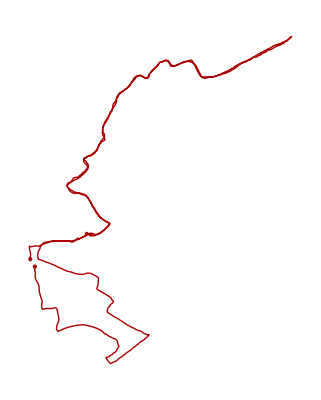

```mathematica
Import["/Users/mchirico/Downloads/CardioTrainer_2011-03-27T13-35-39Z.kml","Graphics"]
```

```mathematica
db=Database`OpenDatabase["/Users/mchirico/db/test.db"];
Database`QueryDatabase[db,"SELECT sqlite_version();"]
```

{{3.6.1}}

```mathematica
Database`QueryDatabase[db,"create table a (a int);"]
```

{}

```mathematica
k:=Database`QueryDatabase[db,"select * from a;"]
k:=Database`QueryDatabase[db,"insert into a (a) values (3424);"]
```

```mathematica
k
```

{{34},{3}}

```mathematica
You may want to take a look at the following:
http://dev.ragfield.com/2009/05/wolframalpha-tweet-analysis.html
```

```mathematica
k:=Database`QueryDatabase[db,"select * from a;"]
```

```mathematica
Plot[k]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[k]

```mathematica
Table[Database`QueryDatabase[db,"insert into a (a) values ("<> ToString[i]<>");"]"i="<>ToString[i],{i,1,230}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
k[[34]]
```

{34}

```mathematica
First[k]
```

{34}

```mathematica
Range[2]
```

{1,2}

```mathematica
ListPlot[,Filling->Axis]
```

ListPlot::lpn: List is not a list of numbers or pairs of numbers.

ListPlot[List,Filling→Axis]

```mathematica
m=Table[k[[i]][[1]],{i,1,200}]
```

{34,3,99,99,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173}

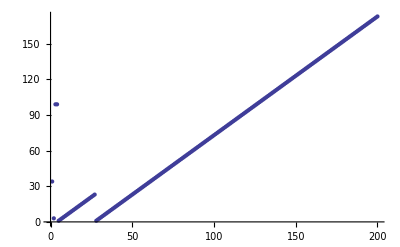

```mathematica
ListPlot[m]
```

```mathematica
DateList["2011-11-19 18:35:26"]
```

```mathematica
{2011,11,19,18,35,26.}
```

```mathematica
DateDifference["2011-11-13 18:45:23","2011-11-19 18:35:26"]
```

5.99309

```mathematica
cmp[x_]:={x*60,x*70,x*75,x*80}
```

```mathematica
cmp[80]
```

{3200,4000,4400}

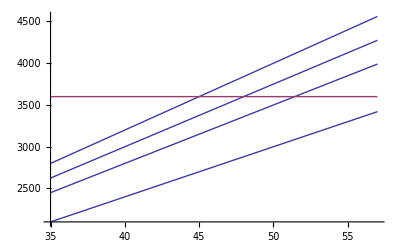

```mathematica
Plot[{cmp[x],3600},{x,35,57}]
```

```mathematica
48*48*75/48
```

3600

```mathematica
48*48*75
```

172800

```mathematica
RunList:={14,20,24,15,28,19,12,21,23,2,11,19,18,23,31,24,24}
```

```mathematica
MovingMedian[RunList,5]
```

{20,20,19,19,21,19,12,19,18,18,19,23,24}

```mathematica
N[MovingMedian[RunList,4]]
```

{17.5,22.,21.5,17.,20.,20.,16.5,16.,15.,14.5,18.5,21.,23.5,24.}

```mathematica
Solve[x^2+a x+1==0,x]
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

```mathematica
$GeoLocation
```

{40.1,-75.11}

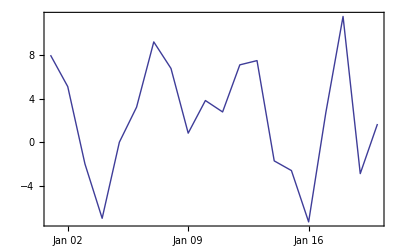

```mathematica
DateListPlot[WeatherData["KPNE", "MeanTemperature", {{2012, 1, 1}, {2012, 12, 31}, "Day"}], Joined->True]
```